## Exemplul 1

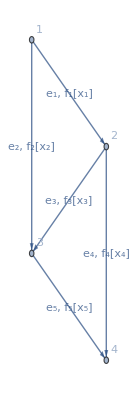

```mathematica
Graph[{Labeled[1->2,"e_1, f_1[x_1]"],Labeled[1->3,"e_2, f_2[x_2]"],Labeled[2->3,"e_3, f_3[x_3]"],Labeled[2->4,"e_4, f_4[x_4]"],Labeled[3->4,"e_5, f_5[x_5]"]},VertexLabels->"Name"]
```

```mathematica
f1[x1_]:=Piecewise[{{x1, x1≤1}, {1, x1>1}, {0, True}}]
f2[x2_]:=Piecewise[{{x2, x2≤1}, {1, x2>1}, {0, True}}]
f3[x3_]:=Piecewise[{{2 x3, x3≤2}, {4, x3>2}, {0, True}}]
f4[x4_]:=Piecewise[{{2 x4, x4≤2}, {4, x4>2}, {0, True}}]
f5[x5_]:=Piecewise[{{2 x5, x5≤2}, {4, x5>2}, {0, True}}]
```

```mathematica
Minimize[{f1[x1]+f2[x2]+f3[x3]+f4[x4]+f5[x5],x1+x2==4,x1-x3-x4==0,x2+x3-x5==0,x4+x5==4,x1≥0,x2≥0,x3≥0,x4≥0,x5≥0},{x1,x2,x3,x4,x5}]
```

{5,{x1→0,x2→4,x3→0,x4→0,x5→4}}

## Exemplul 2

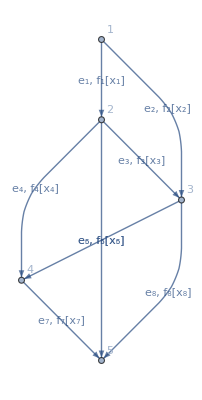

```mathematica
Graph[{Labeled[1->2,"e_1, f_1[x_1]"],Labeled[1->3,"e_2, f_2[x_2]"],Labeled[2->3,"e_3, f_3[x_3]"],Labeled[2->4,"e_4, f_4[x_4]"],Labeled[3->4,"e_5, f_5[x_5]"],Labeled[2->5,"e_6, f_6[x_6]"],Labeled[4->5,"e_7, f_7[x_7]"],Labeled[3->5,"e_8, f_8[x_8]"]},VertexLabels->"Name"]
```

```mathematica
f1[x1_]:=Piecewise[{{x1, x1≤1}, {1, x1>1}, {0, True}}]
f2[x2_]:=Piecewise[{{x2, x2≤1}, {1, x2>1}, {0, True}}]
f3[x3_]:=Piecewise[{{2 x3, x3≤2}, {4, x3>2}, {0, True}}]
f4[x4_]:=Piecewise[{{2 x4, x4≤2}, {4, x4>2}, {0, True}}]
f5[x5_]:=Piecewise[{{x5, x5≤2}, {2, x5>2}, {0, True}}]
f6[x6_]:=Piecewise[{{2 x6, x6≤2}, {4, x6>2}, {0, True}}]
f7[x7_]:=Piecewise[{{x7, x7≤1}, {1, x7>1}, {0, True}}]
f8[x8_]:=Piecewise[{{2 x8, x8≤2}, {4, x8>2}, {0, True}}]
```

```mathematica
Minimize[{f1[x1]+f2[x2]+f3[x3]+f4[x4]+f5[x5]+f6[x6]+f7[x7]+f8[x8],
x1+x2==4,(*1*)
x1-x3-x4-x6==0, (*2*)
x2+x3-x5-x8==0, (*3*)
x4+x5-x7==0, (*4*)
x6+x7+x8==4,(*5*)
x1≥0,x2≥0,x3≥0,x4≥0,x5≥0,x6≥0,x7≥0,x8≥0},{x1,x2,x3,x4,x5,x6,x7,x8}]
```

{4,{x1→0,x2→4,x3→0,x4→0,x5→4,x6→0,x7→4,x8→0}}